```mathematica
Clear[dev,prob,probI,toPS]
```

```mathematica
toPS[x_,y_,ϕ_,R_]:= {x+ (R-y) Tan[ϕ],x-(R+y)Tan[ϕ],-2 y Sqrt[Tan[ϕ]^2+1]}
```

```mathematica
deviation[{xM_,yM_,phiM_},{x_,y_,phi_},R_,sx_,sl_]:=(toPS[xM,yM,phiM,R]-toPS[x,y,phi,R])^2/(2{sx,sx,sl}^2)
```

```mathematica
chiSquared[M_,T_,R_,sx_,sl_]:=Total[deviation[M,T,R,sx,sl]]
```

```mathematica
prob[M_,T_,R_,sx_,sl_]:=1/( (2Pi)^(3/2)sx^2 sl)Exp[-chiSquared[M,T,R,sx,sl]]
```

```mathematica
probIntegrated[M_,{x_,y_},R_,sx_,sl_]:=NIntegrate[prob[M,{x,y,f},R,sx,sl],{f,-Pi/2,Pi/2}]
```

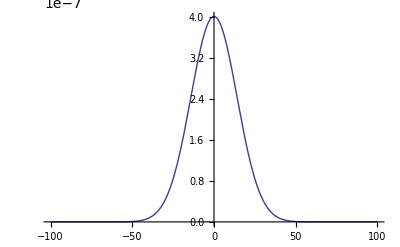

```mathematica
Plot[probIntegrated[{0,0,0},{x,0},350,20,40],{x,-100,100}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

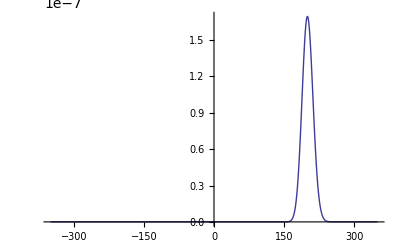

```mathematica
Plot[probIntegrated[{0,200,Pi/4},{0,y},350,20,40],{y,-350,350},PlotRange->All]
```

```mathematica
devT=chiSquared[{xM,yM,phiM},{x,y,phiM+dphi},R,sx,sl]
```

(-x+xM+(R-yM) Tan[phiM]-(R-y) Tan[dphi+phiM])^2/(2 sx^2)+(-x+xM-(R+yM) Tan[phiM]+(R+y) Tan[dphi+phiM])^2/(2 sx^2)+((-2 yM √(1+Tan[phiM]^2)+2 y √(1+Tan[dphi+phiM]^2))^2)/(2 sl^2)

```mathematica
devT2=devT+O[dphi]^3 //Normal //Simplify
```

1/(sl^2 sx^2)(sl^2 x^2-2 sl^2 x xM+sl^2 xM^2+2 dphi sl^2 (-x+xM) y+2 sx^2 y^2+dphi^2 (R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM)))-4 sx^2 y yM+2 sx^2 yM^2-2 (2 dphi sx^2 y (-y+yM)+sl^2 (x (y+dphi^2 y-yM)-xM (y+dphi^2 y-yM)+dphi y (-y+yM))) Tan[phiM]+(2 dphi sl^2 (-x+xM) y+2 dphi^2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM)))+(sl^2+2 sx^2) (y-yM)^2) Tan[phiM]^2-2 dphi y (dphi sl^2 (x-xM)-(sl^2+2 sx^2) (y-yM)) Tan[phiM]^3+dphi^2 (R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)

```mathematica
c=CoefficientList[Collect[devT2,dphi],dphi]
```

{1/(sl^2 sx^2)(sl^2 x^2-2 sl^2 x xM+sl^2 xM^2+2 sx^2 y^2-4 sx^2 y yM+2 sx^2 yM^2-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 sl^2 x yM Tan[phiM]-2 sl^2 xM yM Tan[phiM]+(sl^2+2 sx^2) (y-yM)^2 Tan[phiM]^2),1/(sl^2 sx^2)(2 sl^2 (-x+xM) y-2 sl^2 y (-y+yM) Tan[phiM]-4 sx^2 y (-y+yM) Tan[phiM]+2 sl^2 (-x+xM) y Tan[phiM]^2+2 (sl^2+2 sx^2) y (y-yM) Tan[phiM]^3),1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)}

```mathematica
Integrate[1/((2Pi)^(3/2)sx^2 sl)Exp[-a-b x-d x^2 ],{x,-Infinity,Infinity},Assumptions->d>0]
```

(ⅇ^(-a+b^2/(4 d)))/(2 √2 √d π sl sx^2)

```mathematica
%/.{a->c[[1]],b->c[[2]],d->c[[3]]}
```

ⅇ^(-(sl^2 x^2-2 sl^2 x xM+sl^2 xM^2+2 sx^2 y^2-4 sx^2 y yM+2 sx^2 yM^2-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 sl^2 x yM Tan[phiM]-2 sl^2 xM yM Tan[phiM]+(sl^2+2 sx^2) (y-yM)^2 Tan[phiM]^2)/(sl^2 sx^2)+((2 sl^2 (-x+xM) y-2 sl^2 y (-y+yM) Tan[phiM]-4 sx^2 y (-y+yM) Tan[phiM]+2 sl^2 (-x+xM) y Tan[phiM]^2+2 (sl^2+2 sx^2) y (y-yM) Tan[phiM]^3)^2)/(4 sl^2 sx^2 (R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)))/(2 √2 π sl sx^2 √(1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)))

```mathematica
probIApp[{xM_,yM_,phiM_},{x_,y_},R_,sx_,sl_]=%
```

ⅇ^(-(sl^2 x^2-2 sl^2 x xM+sl^2 xM^2+2 sx^2 y^2-4 sx^2 y yM+2 sx^2 yM^2-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 sl^2 x yM Tan[phiM]-2 sl^2 xM yM Tan[phiM]+(sl^2+2 sx^2) (y-yM)^2 Tan[phiM]^2)/(sl^2 sx^2)+((2 sl^2 (-x+xM) y-2 sl^2 y (-y+yM) Tan[phiM]-4 sx^2 y (-y+yM) Tan[phiM]+2 sl^2 (-x+xM) y Tan[phiM]^2+2 (sl^2+2 sx^2) y (y-yM) Tan[phiM]^3)^2)/(4 sl^2 sx^2 (R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)))/(2 √2 π sl sx^2 √(1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-yM))-2 sl^2 x y Tan[phiM]+2 sl^2 xM y Tan[phiM]+2 (R^2 sl^2+y (sx^2 (4 y-3 yM)+sl^2 (2 y-yM))) Tan[phiM]^2-2 sl^2 (x-xM) y Tan[phiM]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 yM)) Tan[phiM]^4)))

```mathematica
probIApp[{0,0,0},{x,0},R,sx,sy]
```

(ⅇ^(-x^2/sx^2))/(2 √2 π √(R^2/sx^2) sx^2 sy)

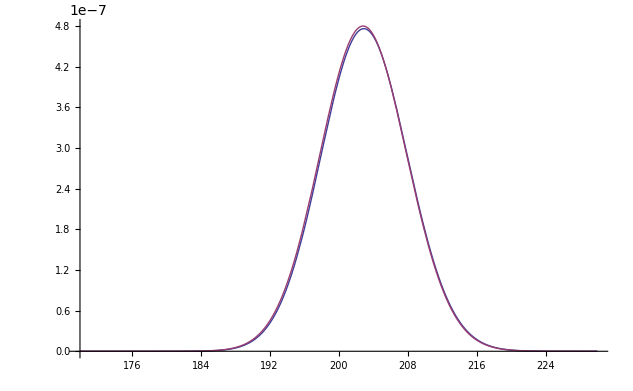

```mathematica
Plot[{probIntegrated[{0,200,Pi/4},{10,y},350,10,15],probIApp[{0,200,Pi/4},{10,y},350,10,15]},{y,170,230},PlotRange->All]
```

```mathematica
mean=NIntegrate[probIntegrated[{0,200,Pi/4},{10,y},350,10,15] y,{y,170,230}]/NIntegrate[probIntegrated[{0,200,Pi/4},{10,y},350,10,15] ,{y,170,230}]
```

203.02

```mathematica
NIntegrate[probIntegrated[{0,200,Pi/4},{10,y},350,10,15] (y-mean)^3,{y,170,230}]/NIntegrate[probIntegrated[{0,200,Pi/4},{10,y},350,10,15] ,{y,170,230}]
```

4.77723

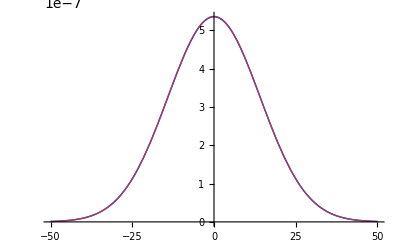

```mathematica
Plot[{probIntegrated[{0,0,0},{x,0},350,20,30],probIApp[{0,0,0},{x,0},350,20,30]},{x,-50,50}]
```